## Zestaw 4

Katarzyna Sowa

## 3N

Zbudowano wielomian interpolacyjny oparty na nastepujacych danych:

```mathematica
Subscript[x, 0]=-1.2300;
Subscript[y, 0]=1.5129;
Subscript[x, 1]=-1.1900;
Subscript[y, 1]=1.4161;
Subscript[x, 2]=-0.7400;
Subscript[y, 2]=0.5476;
Subscript[x, 3]=0.1100;
Subscript[y, 3]=0.0121;
Subscript[x, 4]=2.5600;
Subscript[y, 4]=6.5536;
```

```mathematica
XY={{-1.2300,1.15129},{-1.1900,1.14161},{-0.7400,0.5476},{0.1100,0.0121},{2.5600,6.5536}};
```

```mathematica
Lagrange[XY_,rozm_]:=
Module[{n=rozm-1,wyn,suma=0,resz,X,Y},
X =Transpose[XY]_⟦1⟧;
Y = Transpose[XY]_⟦2⟧; 
Do[wyn = 1; 
Do[ resz = Which[ j==k, 1,
j≠k,(x - X_⟦j+1⟧)/(X_⟦k+1⟧-X_⟦j+1⟧) ]; 
wyn= wyn*resz; ,{j,0,n,1}]; 
suma = suma+ Y_⟦k+1⟧*wyn; ,{k,0,n,1}]; 

Return[Print["Wielomian interpolacyjny: "];
Expand[suma]]; ];
```

```mathematica
Lagrange[XY,5]
```

Wielomian interpolacyjny:

-0.09908+0.700368 x+2.77272 x^2+0.498601 x^3-0.504699 x^4

## 4N

```mathematica
f[x_]:=1/(1+5 x^2);
```

```mathematica
X=Table[x,{x,-1,1,1/32}];
```

Wartosci funkcji w punktach x odpowiednio od -1 do 1 z krokiem 1/32 wynoszą:

```mathematica
Y=Map[f,X]
```

{1/6,1024/5829,256/1381,1024/5229,64/309,1024/4669,256/1101,1024/4149,16/61,1024/3669,256/861,1024/3229,64/189,1024/2829,256/661,1024/2469,4/9,1024/2149,256/501,1024/1869,64/109,1024/1629,256/381,1024/1429,16/21,1024/1269,256/301,1024/1149,64/69,1024/1069,256/261,1024/1029,1,1024/1029,256/261,1024/1069,64/69,1024/1149,256/301,1024/1269,16/21,1024/1429,256/381,1024/1629,64/109,1024/1869,256/501,1024/2149,4/9,1024/2469,256/661,1024/2829,64/189,1024/3229,256/861,1024/3669,16/61,1024/4149,256/1101,1024/4669,64/309,1024/5229,256/1381,1024/5829,1/6}

```mathematica
XY=Transpose[Distribute[{X,Y}]];
```

```mathematica
Lagrange[XY_]:=Module[{j,k,n,X,Y},
Subscript[X, k_] := Transpose[XY]_⟦1,k+1⟧; 
Subscript[Y, k_] := Transpose[XY]_⟦2,k+1⟧; 
n = Length[XY]-1; 
Return[  ∑_(k=0)^n Subscript[Y, k] ( ∏_(j=0)^(k-1) (x-Subscript[X, j])/(Subscript[X, k]-Subscript[X, j]))(∏_(j=k+1)^n (x-Subscript[X, j])/(Subscript[X, k]-Subscript[X, j])) ];];
```

```mathematica
For[n=2,n≤15,n++,
x1=-1;
x2=1;
XXY=N[Table[{x1+(x2-x1)/n k,f[x1+(x2-x1)/n k]},{k,0,n}]];
Cdot=ListPlot[XY,PlotStyle->{Red,PointSize[0.02]}];
P[x_]=Lagrange[XY];
graph1=Plot[f[x],{x,-2,2},PlotStyle->Green];
graph2=Plot[P[x],{x,-1,1},PlotStyle->Blue];
b=Show[graph1,graph2,Cdot]   ]  ;
```

Wykres wielomianu:
kolor niebieski - wykres wielomianu,
kolor zielony - wykres funkcji,
kolor czerwony - wezly i wartosci funkcji.

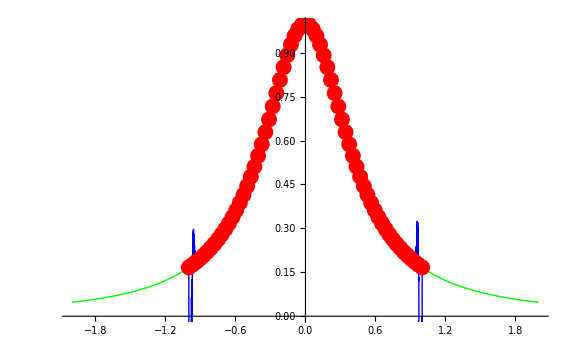

```mathematica
b
```

## 5N

Skonstruowano funckje, jak w zadaniu 4N:

```mathematica
f[x_]:=1/(1+5 x^2);
```

```mathematica
X=Table[x,{x,-1,1,1/32}];
```

```mathematica
Y=Map[f,X];
```

```mathematica
XY=N[Transpose[Distribute[{X,Y}]]];
```

```mathematica
SplajnNat[XY0_] := Module[{XY=XY0}, 
D= Module[{k}, n = Length[XY]-1; X = Transpose[XY]_⟦1⟧; Y = Transpose[XY]_⟦2⟧; h=d = Table[0,{n}]; m = Table[0,{n+1}]; a=b=c=v = Table[0,{n-1}]; s = Table[0,{n},{4}]; 
h_⟦1⟧ = X_⟦2⟧ - X_⟦1⟧; 
d_⟦1⟧ = (Y_⟦2⟧ - Y_⟦1⟧)/h_⟦1⟧; 
For[ k=2, k≤n, k++, 
h_⟦k⟧ = X_⟦k+1⟧ - X_⟦k⟧; 
d_⟦k⟧ = (Y_⟦k+1⟧ - Y_⟦k⟧)/h_⟦k⟧; 
a_⟦k-1⟧ = h_⟦k⟧; 
b_⟦k-1⟧ = 2 (h_⟦k-1⟧ + h_⟦k⟧); 
c_⟦k-1⟧ = h_⟦k⟧; 
v_⟦k-1⟧ = 6 (d_⟦k⟧ - d_⟦k-1⟧)]; ]; 
TrD:=Module[{k,t}, 
m_⟦1⟧ = 0; 
m_⟦n+1⟧ = 0;
For[ k=2, k≤n-1, k++, 
t = a_⟦k-1⟧/b_⟦k-1⟧; 
b_⟦k⟧  =  b_⟦k⟧ - t  c_⟦k-1⟧; 
v_⟦k⟧  =  v_⟦k⟧ - t  v_⟦k-1⟧; ]; 
m_⟦n⟧  =  v_⟦n-1⟧/b_⟦n-1⟧; 
For[ k=n-2, 1≤k, k--, 
m_⟦k+1⟧ = (v_⟦k⟧ - c_⟦k⟧ m_⟦k+2⟧)/b_⟦k⟧; ]; ]; 
Pol:=Module[{k}, 
For[ k=1, k≤n, k++, 
s_⟦k,1⟧ = Y_⟦k⟧; 
s_⟦k,2⟧ = d_⟦k⟧ - 1/6 h_⟦k⟧ (2 m_⟦k⟧+m_⟦k+1⟧); 
s_⟦k,3⟧ = m_⟦k⟧/2; 
s_⟦k,4⟧ = (m_⟦k+1⟧ - m_⟦k⟧)/(6 h_⟦k⟧); ]; ]; 
CS[t_]:=Module[{j}, 
For[ j=1, j≤n, j++, 
If[ X_⟦j⟧≤t && t<X_⟦j+1⟧,k=j ]; ]; 
If[t<X_⟦1⟧,k=1 ]; 
If[X_⟦n+1⟧≤t,k=n ]; 
w = t - X_⟦k⟧; 
Return[ ((s_⟦k,4⟧ w+s_⟦k,3⟧) w+s_⟦k,2⟧) w+s_⟦k,1⟧ ]; ]; 

D; 
TrD; 
Pol; ]
```

Set::wrsym: Symbol D is Protected.

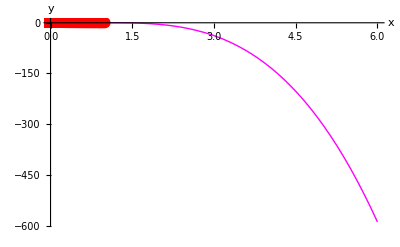

Splajn y = S_i[x]

Punkty = {{-1.,0.166667},{-0.96875,0.175673},{-0.9375,0.185373},{-0.90625,0.195831},{-0.875,0.20712},{-0.84375,0.219319},{-0.8125,0.232516},{-0.78125,0.246806},{-0.75,0.262295},{-0.71875,0.279095},{-0.6875,0.297329},{-0.65625,0.317126},{-0.625,0.338624},{-0.59375,0.361965},{-0.5625,0.387292},{-0.53125,0.414743},{-0.5,0.444444},{-0.46875,0.476501},{-0.4375,0.510978},{-0.40625,0.547887},{-0.375,0.587156},{-0.34375,0.628607},{-0.3125,0.671916},{-0.28125,0.716585},{-0.25,0.761905},{-0.21875,0.806935},{-0.1875,0.850498},{-0.15625,0.89121},{-0.125,0.927536},{-0.09375,0.957905},{-0.0625,0.980843},{-0.03125,0.995141},{0.,1.},{0.03125,0.995141},{0.0625,0.980843},{0.09375,0.957905},{0.125,0.927536},{0.15625,0.89121},{0.1875,0.850498},{0.21875,0.806935},{0.25,0.761905},{0.28125,0.716585},{0.3125,0.671916},{0.34375,0.628607},{0.375,0.587156},{0.40625,0.547887},{0.4375,0.510978},{0.46875,0.476501},{0.5,0.444444},{0.53125,0.414743},{0.5625,0.387292},{0.59375,0.361965},{0.625,0.338624},{0.65625,0.317126},{0.6875,0.297329},{0.71875,0.279095},{0.75,0.262295},{0.78125,0.246806},{0.8125,0.232516},{0.84375,0.219319},{0.875,0.20712},{0.90625,0.195831},{0.9375,0.185373},{0.96875,0.175673},{1.,0.166667}}

Współczynniki:

(0.166667 | 0.28362 | 0 | 4.70397
0.175673 | 0.297402 | 0.440997 | -0.815858
0.185373 | 0.322574 | 0.36451 | 0.708839
0.195831 | 0.347432 | 0.430964 | 0.349951
0.20712 | 0.375393 | 0.463772 | 0.499656
0.219319 | 0.405842 | 0.510614 | 0.516631
0.232516 | 0.439269 | 0.559049 | 0.572019
0.246806 | 0.475886 | 0.612675 | 0.618753
0.262295 | 0.515991 | 0.670684 | 0.667513
0.279095 | 0.559864 | 0.733263 | 0.712503
0.297329 | 0.60778 | 0.80006 | 0.750977
0.317126 | 0.659984 | 0.870464 | 0.777536
0.338624 | 0.716666 | 0.943358 | 0.785085
0.361965 | 0.777926 | 1.01696 | 0.763891
0.387292 | 0.843724 | 1.08857 | 0.701095
0.414743 | 0.913814 | 1.1543 | 0.580113
0.444444 | 0.987657 | 1.20869 | 0.380277
0.476501 | 1.06431 | 1.24434 | 0.0769452
0.510978 | 1.14231 | 1.25155 | -0.357489
0.547887 | 1.21949 | 1.21804 | -0.95104
0.587156 | 1.29283 | 1.12888 | -1.72728
0.628607 | 1.35832 | 0.966946 | -2.69741
0.671916 | 1.41085 | 0.714063 | -3.84901
0.716585 | 1.44421 | 0.353218 | -5.13206
0.761905 | 1.45125 | -0.127913 | -6.44525
0.806935 | 1.42437 | -0.732155 | -7.62808
0.850498 | 1.35626 | -1.44729 | -8.46701
0.89121 | 1.241 | -2.24107 | -8.72375
0.927536 | 1.07538 | -3.05892 | -8.18887
0.957905 | 0.860202 | -3.82663 | -6.75171
0.980843 | 0.601257 | -4.4596 | -4.46351
0.995141 | 0.309456 | -4.87805 | -1.5624
1. | 0 | -5.02453 | 1.5624
0.995141 | -0.309456 | -4.87805 | 4.46351
0.980843 | -0.601257 | -4.4596 | 6.75171
0.957905 | -0.860202 | -3.82663 | 8.18887
0.927536 | -1.07538 | -3.05892 | 8.72375
0.89121 | -1.241 | -2.24107 | 8.46701
0.850498 | -1.35626 | -1.44729 | 7.62808
0.806935 | -1.42437 | -0.732155 | 6.44525
0.761905 | -1.45125 | -0.127913 | 5.13206
0.716585 | -1.44421 | 0.353218 | 3.84901
0.671916 | -1.41085 | 0.714063 | 2.69741
0.628607 | -1.35832 | 0.966946 | 1.72728
0.587156 | -1.29283 | 1.12888 | 0.95104
0.547887 | -1.21949 | 1.21804 | 0.357489
0.510978 | -1.14231 | 1.25155 | -0.0769452
0.476501 | -1.06431 | 1.24434 | -0.380277
0.444444 | -0.987657 | 1.20869 | -0.580113
0.414743 | -0.913814 | 1.1543 | -0.701095
0.387292 | -0.843724 | 1.08857 | -0.763891
0.361965 | -0.777926 | 1.01696 | -0.785085
0.338624 | -0.716666 | 0.943358 | -0.777536
0.317126 | -0.659984 | 0.870464 | -0.750977
0.297329 | -0.60778 | 0.80006 | -0.712503
0.279095 | -0.559864 | 0.733263 | -0.667513
0.262295 | -0.515991 | 0.670684 | -0.618753
0.246806 | -0.475886 | 0.612675 | -0.572019
0.232516 | -0.439269 | 0.559049 | -0.516631
0.219319 | -0.405842 | 0.510614 | -0.499656
0.20712 | -0.375393 | 0.463772 | -0.349951
0.195831 | -0.347432 | 0.430964 | -0.708839
0.185373 | -0.322574 | 0.36451 | 0.815858
0.175673 | -0.297402 | 0.440997 | -4.70397)

```mathematica
SplajnNat[XY];   
dots=ListPlot[XY,PlotStyle->{Red,PointSize[0.02]},DisplayFunction->Identity];  
gr=Plot[CS[x],{x,0,6},PlotStyle->{Magenta},DisplayFunction->Identity];  
Show[gr,dots,AxesLabel->{"x","y    "}] 
Print["Splajn y = ",Subscript[S, i],"[x]"];  
Print["Punkty = ",XY];  
Print["Współczynniki: "]
MatrixForm[Chop[s]]
```